```mathematica
$HistoryLength=0;
ModPlus[l__]:=Mod[Plus[l],2]
```

```mathematica
{{1, 1, 1, 1, 1, 1, 1, 1, 1, □, □, □, □, □, □, □, □, □}, {1, □, □, 1, □, □, 1, 1, □, □, □, □, □, □, □, □, □, □}, {□, 1, □, □, 1, □, □, 1, 1, □, □, □, □, □, □, □, □, □}, {□, □, 1, 1, 1, 1, 1, 1, 1, 1, 1, □, □, □, □, □, □, □}, {□, □, 1, □, □, 1, □, □, 1, 1, □, □, □, □, □, □, □, □}, {□, □, □, 1, □, □, 1, □, □, 1, 1, □, □, □, □, □, □, □}, {□, □, □, □, 1, 1, 1, 1, 1, 1, 1, 1, 1, □, □, □, □, □}, {□, □, □, □, 1, □, □, 1, □, □, 1, 1, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, □, □, □}, {1, 1, 1, 1, 1, 1, □, □, □, □, □, □, □, □, □, □, □, □}, {1, 1, 1, □, □, 1, 1, 1, □, □, □, □, □, □, □, □, □, □}, {1, 1, 1, □, □, □, □, 1, 1, 1, □, □, □, □, □, □, □, □}, {1, 1, 1, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}, {□, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □, □}};
```

```mathematica
x=(7+2n1)+4n2+4;
y=x+(2+n1)(n2+1);
```

```mathematica
yx=(y-x)/x;
```

```mathematica
Plot3D[If[yx>4/7,1,0],{n1,2,10},{n2,0,10},PlotTheme->"Detailed",AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
compare[x_,y_]:=N[(y-x)/y-4/7];
rate[x_,y_]:=(y-x)/y//N;
```

```mathematica
altParam=Sort[Flatten[Select[Abs[rate[#⟦3⟧,#⟦4⟧]-4/7]≤.1∧#⟦3⟧≤64∧#⟦4⟧-#⟦3⟧≤64& ]/@Table[{n1,n2,BuildHt["dim"]["x",n1,n2],BuildHt["dim"]["y",n1,n2],rate[BuildHt["dim"]["x",n1,n2],BuildHt["dim"]["y",n1,n2]]},{n1,2,100},{n2,0,100} ],1],#1⟦4⟧<#2⟦4⟧& ]//DeleteDuplicates[#,#1⟦4⟧===#2⟦4⟧&]&
```

{{7,3,40,76,0.473684},{11,2,43,82,0.47561},{6,4,43,83,0.481928},{12,2,45,87,0.482759},{9,3,44,88,0.5},{7,4,45,90,0.5},{13,2,47,92,0.48913},{10,3,46,94,0.510638},{6,5,48,96,0.5},{14,2,49,97,0.494845},{11,3,48,100,0.52},{15,2,51,102,0.5},{9,4,49,104,0.528846},{12,3,50,106,0.528302},{16,2,53,107,0.504673},{6,6,53,109,0.513761},{10,4,51,111,0.540541},{17,2,55,112,0.508929},{4,8,59,113,0.477876},{18,2,57,117,0.512821},{14,3,54,118,0.542373},{19,2,59,122,0.516393},{5,8,61,124,0.508065}}

```mathematica
BuildHt["dim"][xy:("x"|"y"),n1_,n2_]:=With[{x=(7+2n1)+5n2+4,yParcial=(2+n1)(n2+1)},<|"x"->x,"y"->x+yParcial|>[xy]]
```

```mathematica
BuildHt[n1Usado_,n2Usado_]:=Block[{n1,n2,blocoInterno,alturaBloco,xUsado,yUsado,bloco,todosBlocos,parteAlta,Ht,Gt},
{blocoInterno,alturaBloco,xUsado,yUsado}={7+2n1,2+n1,BuildHt["dim"]["x",n1,n2],BuildHt["dim"]["y",n1,n2]}/.{n1->n1Usado,n2->n2Usado};
bloco[ind_]:=Join[{PadRight[Table[1,blocoInterno],xUsado-4]},Table[PadRight[Join[RotateLeft[{1,1,1,0},3Mod[ind,2]+(-1)^Mod[ind,2] Abs[3-Mod[i,7]]],Table[0,2 i],{1,1,1}],xUsado-4],{i,0,alturaBloco-2}]];
todosBlocos=Join@@Table[RotateRight[bloco[i],{0,5i}],{i,0,n2Usado}];
parteAlta=PadLeft[todosBlocos,{Length@todosBlocos,xUsado},1];
Ht=Join[parteAlta,IdentityMatrix[xUsado]];
Gt=Transpose@Join[IdentityMatrix[yUsado-xUsado],parteAlta,2];
{Ht,Gt}
]
```

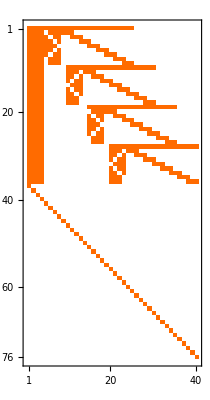
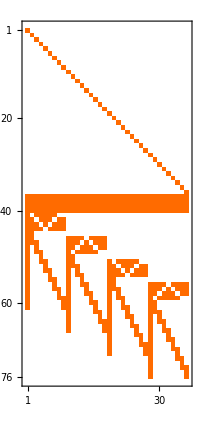
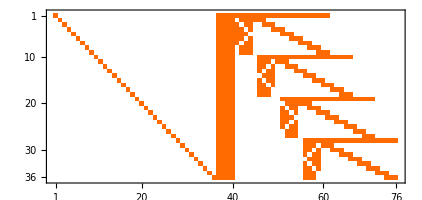

```mathematica
{Ht,Gt}=BuildHt[7,3];
MatrixPlot/@{Ht,Gt,Transpose@Gt}
```

```mathematica
Map[MatrixPlot@Map[Function[line,If[line∈#,line/.{0->Green,1->Blue},line]],Ht]& ]@Select[Subsets[Ht,{4}],Plus@@ModPlus@@#==0& ]
```

{}

```mathematica
ToInteger[list_]:=Plus@@MapIndexed[#1 2^(Length@list-First@#2)&,list];
```

```mathematica
ToInteger[Ht⟦36⟧~ModPlus~Ht⟦37⟧]
```

481038172167

```mathematica
ToInteger[RotateRight[#,-1]&@Join[{1},Table[0,35]]]
```

1

```mathematica
Benchmark[n1n2Pairs:{({_Integer,_Integer})..},maxWeight_Integer]:=Block[{Ht,Gt,nInfo,done=0},
SetDirectory[NotebookDirectory[]];
Map[Function[{n1,n2},
{Ht,Gt}=BuildHt[n1,n2];
nInfo=BuildHt["dim"]["y",n1,n2]-BuildHt["dim"]["x",n1,n2];
Export["dados/Ht.csv",Ht];
Export["dados/Gt.csv",Gt];
Export["dados/amostra-informacao.csv",Table[RandomChoice[{0,1}, nInfo],Ceiling[1000000/nInfo] ] ];
Run[StringJoin@{ "./benchmark ",ToString@maxWeight," temp/result-"<>ToString@n1<>"-"<>ToString@n2<>".csv"}];
done=done+1;
][#⟦1⟧,#⟦2⟧]&,n1n2Pairs]~Monitor~done;
<|
"p"->Flatten@Import["dados/lista-de-p.csv"],
"errorRates"->(Flatten@Import["temp/result-"<>ToString@#⟦1⟧<>"-"<>ToString@#⟦2⟧<>".csv"]&/@n1n2Pairs),
"n1n2Pairs"->n1n2Pairs
|>
]
```

```mathematica
altParamBenchmark=Benchmark[Take[#,2]&/@altParam,3]
```

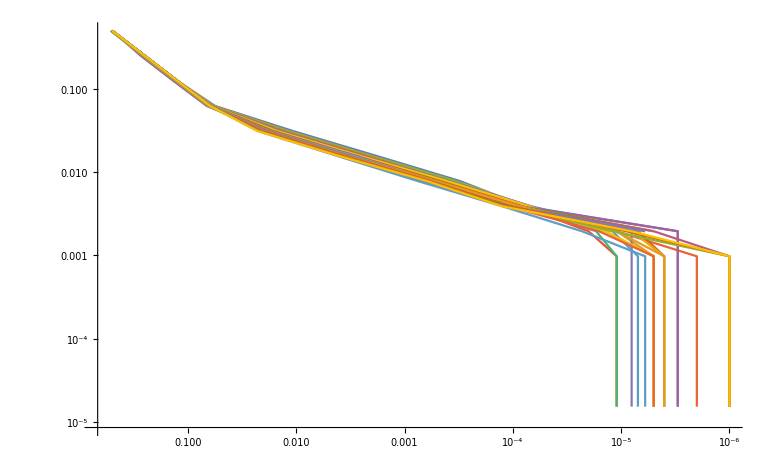

```mathematica
ListLinePlot[Partition[#,2]&@Riffle[#,ps]&/@altParamBenchmark,ScalingFunctions->{{-Log@#&,E^-#&},{Log@#&,E^#&}}]
```

## n1 de 2 a 8; n2 de 0 a 8

```mathematica
ParallelTable[Length@Select[Subsets[BuildHt[n1,n2],{4}],Plus@@ModPlus@@#==0& ],{n1,5,8},{n2,0,8}]
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

```mathematica
Select[Subsets[First@BuildHt[7,3],{5}],Plus@@ModPlus@@#==0& ]
```

$Aborted

## Exportação de dados

```mathematica
SetDirectory[NotebookDirectory[]]
```

/media/vitor/000F8EFA0002DB72/ITA/ELE32/lab1

```mathematica
Export["dados/Ht.csv",Ht];
```

```mathematica
Export["dados/Gt.csv",Gt];
```

```mathematica
amostras=Partition[RandomChoice[{0,1}, 40000 36],36];
```

```mathematica
Export["dados/amostra-informacao.csv",amostras];
```

## Importação de resultados (MATLAB)

```mathematica
SetDirectory[NotebookDirectory[]]
```

/media/vitor/000F8EFA0002DB72/ITA/ELE32/lab1

```mathematica
<<MATLink`
```

```mathematica
OpenMATLAB[]
```

```mathematica
MEvaluate["cd '/media/vitor/000F8EFA0002DB72/ITA/ELE32/lab1'"]
```

```mathematica
MEvaluate["Lab1"]
```

```mathematica
MEvaluate["load 'matlab-workspace'"]
```

```mathematica
MGet["chances"]
```

{0.666735,0.348607,0.129027,0.0390427,0.0106227,0.00291533,0.000677333,0.000176,0.000046,0.0000153333,3.33333×10^-6,1.33333×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
{chances[2],chances[3],chances[4],chances[5]}=Flatten@Import["dados-7-3/taxa-erro-d"<>#<>".csv"]&/@{"2","3","4","5"}
```

{{0.500031,0.500031,0.250016,0.125006,0.0610057,0.0200637,0.00508538,0.00120361,0.000299375,0.0000769792,0.0000195833,5.69444×10^-6,1.04167×10^-6,5.55556×10^-7,2.77778×10^-7,2.43056×10^-7,2.08333×10^-7,3.47222×10^-8,0,0},{0.500031,0.500031,0.250016,0.125006,0.0561227,0.0107067,0.00180545,0.000313542,0.000064375,5.79861×10^-6,1.38889×10^-6,3.47222×10^-7,1.04167×10^-7,1.04167×10^-7,1.04167×10^-7,1.04167×10^-7,1.04167×10^-7,0,0,0},{0.500031,0.500031,0.250016,0.125037,0.0462518,0.00485028,0.000515104,0.0000767014,0.0000114931,1.00694×10^-6,1.38889×10^-7,0,0,0,0,0,0,0,0,0},{0.500031,0.500031,0.250014,0.125133,0.027583,0.00179889,0.000161944,0.0000279861,4.93056×10^-6,8.33333×10^-7,1.38889×10^-7,0,0,0,0,0,0,0,0,0}}

```mathematica
ps=Flatten@Import["dados/lista-de-p.csv"]
```

{0.5,0.25,0.125,0.0625,0.03125,0.015625,0.0078125,0.00390625,0.00195312,0.000976562,0.000488281,0.000244141,0.00012207,0.0000610352,0.0000305176,0.0000152588,7.62939×10^-6,3.8147×10^-6,1.90735×10^-6}

```mathematica
MSet["chances_nosso_2",chances[2]];
MSet["chances_nosso_3",chances[3]];
MSet["chances_nosso_4",chances[4]];
MSet["chances_nosso_5",chances[5]];
MSet["p_nosso",ps];
MSet["altParam",altParam];
MSet["altParamBenchmark",altParamBenchmark];
```

```mathematica
MEvaluate["
figure;
h1=axes;
loglog(p_nosso,altParamBenchmark(1,:));
set(h1, 'Xdir', 'reverse');
"]
```

```mathematica
MEvaluate["
figure
h1 = axes;
loglog(...
	p_nosso, p(1:length(p_nosso)), '-o',...
	p, chances, '-*',...
	p_nosso, chances_nosso_2, '-^',...
	p_nosso, chances_nosso_3, '-x',...
	p_nosso, chances_nosso_4, '-s',...
	p_nosso, chances_nosso_5, '-d',...
	'MarkerIndices', [8] ...
);
set(h1, 'Xdir', 'reverse');
legend('Sem código','Hamming','N[7,3] e w=2','N[7,3] e w=3','N[7,3] e w=4','N[7,3] e w=5');
xlabel('Probabilidade de Erro do Canal (p)');
ylabel('Probabilidade de Erro de Bit de Informação');
title('Análise comparativa Hamming-N[7,3]');
"]
```

MATLink::errx: Undefined function or variable 'label'.
     
     Error in input (line 18)
     label

$Failed

```mathematica
MEvaluate["help labels"]
```

>> 
labels not found.

Use the Help browser search field to search the documentation, or
type "help help" for help command options, such as help for methods.

```mathematica
Quiet@Remove["Global`x","Global`y","Global`n","Global`p"];
```

```mathematica
f[n_,p_,x_]:=Binomial[n,x] p^x(1-p)^(n-x)
```

```mathematica
F[n_,p_,x_]:=(1-p)^n ((1/(1-p))^n-(1-p)^(-1-x) p^(1+x) Binomial[n,1+x] Hypergeometric2F1[1,1-n+x,2+x,p/(-1+p)])
```

```mathematica
g[v_,n_,p_,x_,z_]:=Binomial[v,z] ((1-p)^n ((1/(1-p))^n-(1-p)^(-1-x) p^(1+x) Binomial[n,1+x] Hypergeometric2F1[1,1-n+x,2+x,p/(-1+p)]))^z (1-(1-p)^n ((1/(1-p))^n-(1-p)^(-1-x) p^(1+x) Binomial[n,1+x] Hypergeometric2F1[1,1-n+x,2+x,p/(-1+p)]))^(v-z)
```

h[v_,n_,p_,x_]:=Sum[i g[v,n,p,x,i],{i,0,v}]

```mathematica
h[v_,n_,p_,x_]:=((1-p)^(n-x) v (-(((1-p)^x (-1+p) (1+x))/((1-p)^x-(1/(1-p))^n (1-p)^(n+x)-(1-p)^x p+(1/(1-p))^n (1-p)^(n+x) p+(1-p)^x x-(1/(1-p))^n (1-p)^(n+x) x-(1-p)^x p x+(1/(1-p))^n (1-p)^(n+x) p x+n (1-p)^n p^(1+x) Binomial[n,x] Hypergeometric2F1[1,1-n+x,2+x,p/(-1+p)]-(1-p)^n p^(1+x) x Binomial[n,x] Hypergeometric2F1[1,1-n+x,2+x,p/(-1+p)])))^v ((1-p)^x-(1/(1-p))^n (1-p)^(n+x)-(1-p)^x p+(1/(1-p))^n (1-p)^(n+x) p+(1-p)^x x-(1/(1-p))^n (1-p)^(n+x) x-(1-p)^x p x+(1/(1-p))^n (1-p)^(n+x) p x+n (1-p)^n p^(1+x) Binomial[n,x] Hypergeometric2F1[1,1-n+x,2+x,p/(-1+p)]-(1-p)^n p^(1+x) x Binomial[n,x] Hypergeometric2F1[1,1-n+x,2+x,p/(-1+p)]) (-(1/(1-p))^n (1-p)^x+(1/(1-p))^n (1-p)^x p+p^(1+x) Binomial[n,1+x] Hypergeometric2F1[1,1-n+x,2+x,p/(-1+p)]) (1-(1-p)^n ((1/(1-p))^n-(1-p)^(-1-x) p^(1+x) Binomial[n,1+x] Hypergeometric2F1[1,1-n+x,2+x,p/(-1+p)]))^v)/((-1+p) (1+x) ((1-p)^x-(1/(1-p))^n (1-p)^(n+x)-(1-p)^x p+(1/(1-p))^n (1-p)^(n+x) p+(1-p)^n p^(1+x) Binomial[n,1+x] Hypergeometric2F1[1,1-n+x,2+x,p/(-1+p)]))
```

```mathematica
i[v_,n_,p_]:=1-(n h[v,n,p,2]+(v-h[v,n,p,2])n (1-p))/(n v)
```

```mathematica
taxasDeErro=N@Map[i[40000,36,#]&][SetPrecision[ps,Infinity]];
```

```mathematica
psComTaxas=Partition[#,2]&@Riffle[1/ps,taxasDeErro];
```

```mathematica
psComTaxasMedidos=Partition[#,2]&@Riffle[1/ps,chances];
```

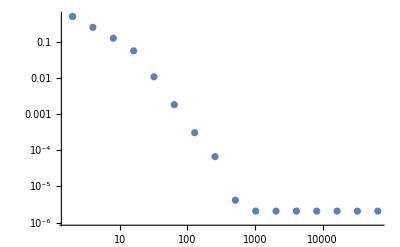

```mathematica
ListLogLogPlot[psComTaxasMedidos]
```

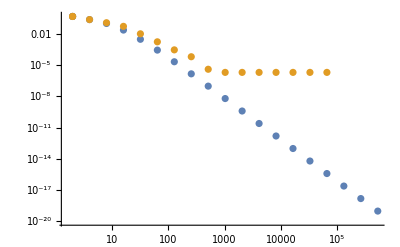

```mathematica
ListLogLogPlot[{psComTaxas,psComTaxasMedidos},PlotRange->All]
```

```mathematica
fit=Fit[Log@psComTaxas,{1,x},x]
```

4.95298-3.59001 x

```mathematica
Fit[Log@psComTaxasMedidos,{1,x},x]
```

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Fit[{{0.693147,-0.693045},{0.693147,-0.693045},{1.38629,-1.38605},{2.07944,-2.0794},{2.77259,-2.88224},{3.46574,-4.53388},{4.15888,-6.30923},{4.85203,-8.09338},{5.54518,-9.6158},{6.23833,-12.3884},{6.93147,-13.0815},{7.62462,-13.0815},{8.31776,-13.0815},{9.01092,-13.0815},{9.70406,-13.0815},{10.3972,-13.0815},{11.0904,-13.0815},{11.7835,-∞},{12.4766,-∞},{13.1698,-∞}},{1,x},x]

```mathematica
MSet["altParam",Part[#,4]&/@altParam]
```

```mathematica
MGet["altParam"]
```

{76.,82.,83.,87.,88.,90.,92.,94.,96.,97.,100.,102.,104.,106.,107.,109.,111.,112.,113.,117.,118.,122.,124.}

```mathematica
MSet["ps",ps];
```

```mathematica
MEvaluate["
X=zeros(length(ps),length(altParam));
Y=X;
Z=X;
for i=1:length(ps)
	for j=1:length(altParam)
		X(i,j)=ps(i);
		Y(i,j)=altParam(j);
		Z(i,j)=altParamBenchmark(j,i);
	end
end
surf(X,Y,Z);
set(gca, 'XScale', 'log', 'YScale', 'linear', 'ZScale', 'log')
"]
```

```mathematica
MEvaluate["
figure;
h1 = axes;
escolhidos=[1 4 10 15 20 23];
escolhidos_reverso=escolhidos(end:-1:1);
markers=['-o', '-^', '-s', '-x', '-d', '-p'];
for i=length(escolhidos):-1:1
	loglog(ps, altParamBenchmark(escolhidos(i),:), markers(2*i-1:2*i), 'MarkerIndices', 6+(1-(-1)^i)/2);
	hold on;
end
loglog(p_nosso, p(1:length(p_nosso)), '-.');
legend(cellstr(int2str(altParam(escolhidos_reverso)')), 'Sem código');
xlabel('Probabilidade de Erro do Canal (p)');
ylabel('Probabilidade de Erro de Bit de Informação');
title('Desempenho da Família N com Diferentes Tamanhos de Bloco');
set(h1, 'Xdir', 'reverse');
"]
```